FastICA Uniform

```mathematica
x=RandomReal[{-Sqrt[3],Sqrt[3]},1000];
y=RandomReal[{-Sqrt[3],Sqrt[3]},1000];
A={{5,10},{10,2}};
mt=A.{x,y};
mt=mt-Mean[Transpose[mt]];
```

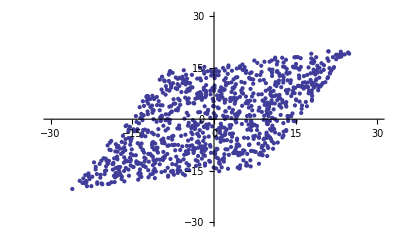

```mathematica
ma=Transpose[mt];
ListPlot[{ma[[All]]},PlotRange->{{-30,30},{-30,30}}]
```

```mathematica
Covariance[Transpose[mt]]
```

{{127.612,71.6628},{71.6628,103.595}}

```mathematica
Eigenvalues[Covariance[Transpose[mt]]]
```

{188.265,42.9412}

```mathematica
Eigenvectors[Covariance[Transpose[mt]]]
```

{{-0.763304,-0.646039},{0.646039,-0.763304}}

```mathematica
d12=1/Sqrt[Eigenvalues[Covariance[Transpose[mt]]][[1]]]
d22=1/Sqrt[Eigenvalues[Covariance[Transpose[mt]]][[2]]]
dmat=DiagonalMatrix[{d12,d22}]
```

0.0728811

0.152603

{{0.0728811,0.},{0.,0.152603}}

```mathematica
emat=Transpose[Eigenvectors[Covariance[Transpose[mt]]]]
```

{{-0.763304,0.646039},{-0.646039,-0.763304}}

```mathematica
vmat=emat.dmat.Transpose[emat]
```

{{0.106154,-0.0393128},{-0.0393128,0.11933}}

```mathematica
x=RandomReal[{-Sqrt[3],Sqrt[3]},1000];
y=RandomReal[{-Sqrt[3],Sqrt[3]},1000];
mt=A.{x,y};
mt=mt-Mean[Transpose[mt]];
```

```mathematica
zmat=vmat.mt;
```

```mathematica
mt //MatrixForm
vmat //MatrixForm
```

(1.90996 | 1.37303 | -11.5021 | -6.1262 | -15.7276 | 3.78445 | -1.87202 | 8.34705 | 5.13663 | 8.88288 | -11.5923 | 3.7345 | 19.9937 | -17.684 | -10.721 | -7.74945 | 3.3351 | 19.2943 | 17.5261 | -3.16647 | 9.91213 | 2.50445 | 0.842391 | -4.81282 | -1.73702 | -1.22549 | -14.033 | 6.86118 | 4.96929 | 2.23354 | 5.21791 | 3.46307 | 14.542 | -6.76119 | -9.43789 | -21.5968 | 0.511165 | 8.12301 | 12.8911 | 12.8316 | 12.2147 | 17.2932 | -17.8542 | -18.0557 | 13.8037 | -19.677 | -11.4947 | -7.31336 | 11.087 | -1.14534 | -1.75442 | -7.15363 | -11.4316 | -3.88351 | -0.547843 | 4.30636 | -10.6867 | 8.52073 | -11.2328 | 10.6437 | -8.26524 | 11.4976 | -9.19797 | 6.02645 | -18.6857 | -2.45432 | -3.36764 | -6.60669 | 13.8539 | -17.9874 | 14.7014 | 16.5626 | 0.488636 | -3.56849 | 5.00833 | -17.2226 | 7.00792 | 2.88516 | 17.9432 | 6.41426 | -17.3398 | 8.07183 | 6.1351 | 20.1657 | -7.89758 | -3.3719 | 4.66265 | 1.2718 | 15.9894 | 1.06819 | 2.66123 | 0.287981 | 17.3598 | 2.71865 | -7.83921 | -7.08948 | -11.8323 | 5.20011 | 8.89667 | 3.95158 | -15.3963 | -14.0052 | -13.5641 | 19.2413 | -0.449786 | -7.49198 | 10.561 | -0.537665 | -22.3289 | -10.9691 | -5.58082 | 3.03275 | 1.71092 | 23.1739 | -20.0857 | 0.659417 | 3.87482 | 19.059 | -14.2982 | -20.7025 | 3.78633 | 20.8061 | -2.33504 | 6.46966 | -9.07833 | -6.56593 | -3.01464 | 15.4037 | 15.3964 | 19.3471 | 5.55072 | 14.3102 | 9.98046 | -3.2608 | -7.17794 | -12.8673 | 13.0357 | 9.4994 | 10.3405 | 6.82929 | 1.15059 | -1.41631 | -7.21006 | -6.71856 | 12.9248 | -3.09768 | -9.64567 | -11.952 | 12.7275 | 15.3586 | 4.32411 | 5.68555 | 10.1868 | 11.1025 | 20.5266 | -12.4974 | 11.9082 | 7.55108 | 13.5335 | 5.056 | -9.10477 | 21.4662 | -13.2455 | -7.36122 | 15.9906 | 18.0754 | 8.26746 | 11.3111 | 4.94718 | -9.05224 | -9.9689 | -15.1039 | -2.96232 | -3.80511 | 12.4456 | 16.8731 | -13.1732 | 6.85302 | -6.53733 | -14.4138 | 6.46699 | 0.381015 | -11.5882 | 10.7341 | 21.574 | -12.7728 | -9.14387 | -17.4878 | -3.96013 | -2.94602 | -4.19747 | -9.41758 | -7.16423 | -8.90065 | 3.04932 | -9.2191 | 4.27707 | -4.11835 | -9.89316 | 9.49895 | 12.1152 | -8.53123 | -9.8155 | -2.81857 | -24.2825 | 10.9333 | -8.1415 | 4.3171 | -20.8229 | 7.7979 | -13.7262 | 1.22009 | 3.40296 | -7.62595 | 2.40873 | -3.75955 | -7.16968 | 6.52972 | 18.3768 | -5.09834 | 0.414193 | -2.63996 | -20.6827 | -8.65728 | 2.93633 | 10.6756 | 17.904 | -13.636 | 14.6682 | 0.114652 | -14.4825 | 9.46803 | -1.0293 | -4.29639 | 3.50167 | -8.37876 | 18.6246 | 4.54229 | 10.5273 | 14.0635 | 16.0674 | -12.4209 | -12.3974 | -7.15377 | -24.1884 | 14.1942 | -1.00926 | -8.0147 | 6.94282 | 7.21647 | 6.21483 | -12.387 | -1.94248 | 4.97055 | -5.91155 | 15.5291 | -23.3938 | 9.39845 | 10.153 | -1.18091 | -2.30171 | -22.6959 | -5.93576 | -0.67351 | 11.4309 | -2.67183 | 7.06789 | -18.3749 | -15.3495 | -12.7808 | -9.04295 | 5.2782 | 10.9523 | 9.54137 | 6.05128 | 22.4803 | -1.28535 | -1.01424 | 7.09244 | -12.1126 | 8.28621 | 15.4959 | -6.40823 | 14.101 | -3.19908 | -3.09545 | 17.7529 | -2.16874 | -6.22617 | 6.86333 | -20.199 | 7.93647 | -24.3527 | -4.79547 | -13.2035 | 19.6485 | 0.925757 | 6.88387 | 16.8093 | 2.68145 | -0.6097 | -8.63169 | 2.53641 | 13.24 | -16.3231 | -6.4132 | 20.0712 | 8.44782 | 13.9802 | 4.84399 | 9.46916 | 15.3743 | 0.717426 | -17.1688 | 12.0647 | 18.1085 | 0.318161 | -5.8572 | 0.359183 | -10.7006 | 8.6243 | 2.85922 | 5.4965 | -3.2137 | -22.9882 | 18.1187 | -7.47988 | -5.34761 | -4.24062 | 5.73586 | -12.8202 | 18.5259 | 14.8026 | 0.942711 | -8.16626 | -10.776 | 4.12915 | -9.70647 | 2.24901 | -16.1742 | 4.66551 | 16.1349 | -15.9722 | -12.9046 | 11.3336 | -3.65621 | -13.4655 | -0.275868 | 9.92924 | -8.10019 | 7.52241 | -6.46975 | 17.7423 | 16.4166 | 8.6549 | 4.5369 | 7.63402 | 21.8823 | -14.3249 | -5.05641 | -21.8969 | 4.32281 | -9.39256 | -10.8511 | -15.2726 | 3.16086 | -14.5386 | 17.3042 | 21.9662 | 11.0158 | -10.4046 | -15.921 | -15.6025 | 4.5423 | 19.5712 | 13.9703 | 9.06454 | 1.67777 | -14.8512 | 8.69192 | -18.9992 | -4.52287 | 8.14595 | -3.18848 | -12.1602 | -24.6892 | 8.55861 | -14.2277 | -6.76647 | 3.98092 | -19.5187 | -14.6106 | 0.67434 | 14.3218 | -8.51338 | -11.1511 | -12.8583 | 21.8254 | 5.56253 | 3.72259 | -16.7747 | 5.78809 | -1.65395 | 6.3162 | 7.3979 | 15.2256 | -9.07085 | -5.86556 | 3.09054 | -10.6968 | -12.7261 | 4.25955 | -3.5911 | -1.9297 | -9.92565 | 9.95553 | 12.3796 | 9.09357 | -12.2439 | 3.97981 | -8.30244 | -14.2217 | -7.22228 | -4.76411 | -8.01917 | -12.6599 | 9.01072 | 18.5829 | -10.6043 | -2.40088 | -8.19624 | -4.06314 | 10.1253 | 16.6939 | -12.9355 | -24.4765 | -0.769756 | 14.8994 | 16.8203 | -5.53371 | -14.2594 | -11.5765 | 17.4756 | -19.633 | 7.54786 | -22.7954 | 15.6028 | 7.27929 | -0.882369 | 22.4885 | -11.2454 | -10.7568 | -18.0182 | 17.8149 | -10.1821 | -0.415346 | -17.8069 | 11.145 | -23.773 | 1.47332 | -4.99592 | -23.4522 | -1.45464 | -15.4823 | -14.9131 | 0.217997 | -0.882096 | 17.5071 | -7.64656 | -0.896579 | -2.89798 | 2.7729 | 8.07433 | 15.5329 | 6.73223 | -5.92863 | 13.0109 | 1.49552 | -7.34617 | -8.74253 | 20.0106 | -7.56161 | 13.9074 | 2.98424 | 0.436098 | 14.5489 | -3.15219 | 11.296 | -8.45898 | -5.23259 | -15.4954 | -11.0259 | 1.03506 | -6.25179 | 15.2168 | -5.37871 | 4.91578 | 7.9564 | -5.32151 | 24.3267 | -15.7629 | 20.2397 | 8.26806 | -0.84138 | 6.32517 | 3.06672 | -13.3563 | 7.90724 | 12.3676 | -1.14388 | -9.91697 | -3.47867 | 12.2373 | 7.57366 | 9.73908 | 22.477 | 3.08303 | -5.54214 | 6.31038 | -5.22691 | 19.4186 | -25.0528 | -0.24678 | 14.7816 | 2.76616 | 10.2782 | 0.567649 | 13.7717 | -4.24328 | -11.5672 | -5.33334 | -22.4602 | 10.055 | -11.2756 | 7.14991 | 15.0604 | 3.84118 | -12.8055 | 2.1165 | -5.8091 | 4.51718 | -17.318 | -5.43179 | 18.0758 | 7.15173 | 14.0252 | 17.9578 | -7.6879 | -17.959 | -3.35775 | 3.59424 | 17.2812 | -18.4973 | -2.03545 | 2.42938 | 15.4133 | -9.86184 | 8.70468 | -2.34543 | 13.4993 | 9.23876 | -14.4168 | -13.5435 | -12.2963 | 16.4115 | -12.3699 | -24.34 | 12.3304 | -16.6408 | -0.333425 | 7.45347 | -8.31885 | -20.6259 | 14.2317 | -9.02211 | 4.63517 | 3.29511 | 3.93097 | -19.6097 | 15.492 | -5.65884 | -11.0253 | 11.0213 | -12.9675 | -21.011 | 14.3426 | 15.8605 | -11.8491 | -0.414088 | -7.44239 | 15.7894 | -0.613831 | 21.9081 | 2.50268 | 9.26669 | 12.5111 | 0.999132 | -10.3596 | 12.3227 | -7.21911 | 12.6192 | 7.96174 | -16.9925 | -11.9596 | -4.42682 | 17.5012 | 13.1576 | 10.0824 | -5.88282 | 11.9069 | -5.86103 | 24.6274 | -16.0129 | 20.9739 | 7.95798 | 13.3678 | 11.0097 | 2.77155 | 3.43753 | 5.35185 | -10.6175 | -13.0108 | -10.9544 | -24.2729 | 14.2038 | -15.6965 | 10.4594 | 9.00496 | 6.02662 | 5.12257 | 11.4737 | 11.1416 | 10.0994 | 2.75719 | 6.91716 | -3.43025 | -1.68707 | -0.975709 | -14.6808 | 24.9073 | -11.4664 | -5.83104 | -7.41204 | 11.9198 | 8.67562 | 6.15725 | -8.83852 | 16.4318 | -1.12344 | 6.12223 | -21.0282 | -1.34546 | 3.06436 | -19.7031 | 5.53842 | -9.59893 | 1.22718 | -5.64666 | -9.06052 | 15.566 | -3.92841 | 6.90687 | -9.75548 | 7.405 | -16.155 | 1.20967 | -5.3663 | -8.29971 | 22.3948 | 3.09521 | -6.53566 | 7.29652 | -2.35955 | -4.32606 | 5.0396 | 7.15467 | -1.46051 | -7.84045 | -10.271 | 20.6621 | -22.8094 | -2.30804 | -3.30124 | -15.7881 | 5.44957 | 4.01324 | -0.142504 | -10.642 | -9.13673 | 2.5224 | 21.1923 | -12.6604 | -8.54956 | 0.740977 | 1.88237 | 6.85396 | 10.2819 | 9.70031 | 0.998434 | -12.6305 | -16.466 | 8.05308 | -1.97893 | 8.3925 | -18.1925 | -15.4601 | -14.8859 | 7.69231 | 3.02058 | -2.52162 | 18.4454 | 16.1593 | -16.4246 | 11.4004 | -10.2877 | 10.6876 | -7.94326 | 24.6271 | -16.7778 | 6.16601 | 1.39183 | -13.3827 | -1.20694 | -21.0827 | 9.63014 | -17.9907 | 8.86516 | -14.7975 | -4.87743 | -2.89988 | 4.26468 | -13.4852 | -2.34904 | -3.4076 | -11.2095 | 7.6367 | -3.19218 | 9.7377 | -6.8214 | 4.98666 | -12.949 | 4.64224 | 1.88516 | -1.19952 | 15.8692 | -16.9867 | -2.65003 | 16.5613 | 13.511 | -7.59728 | -4.6993 | -7.92957 | 2.7774 | 20.8156 | 6.22967 | -4.66486 | 21.2177 | -10.5153 | 12.0023 | -6.94905 | 5.01533 | 2.23656 | -0.0190797 | 3.73523 | 8.37921 | -15.9361 | -4.3833 | -12.6259 | 12.1116 | -6.33904 | -3.44923 | -8.51778 | 6.62804 | 20.3514 | 3.30214 | 14.3229 | -11.8781 | 7.4752 | -7.61205 | -9.90694 | -1.21749 | -7.09206 | -4.72576 | -16.7246 | -13.7456 | 3.95945 | 5.33835 | -2.35182 | -2.28218 | 10.7305 | 7.7004 | -11.9139 | -2.2975 | -18.7944 | -13.5423 | -11.0595 | -8.80774 | 8.44422 | -13.4973 | 11.9377 | -1.16102 | 12.2503 | -24.3093 | 20.0844 | 11.6689 | -2.94468 | -9.54925 | 17.2878 | -5.10267 | -5.43808 | -9.1112 | 2.02643 | -15.4205 | -2.91135 | -8.56102 | -5.17448 | 3.64331 | 16.4088 | -9.04793 | -18.0144 | -11.0353 | 17.229 | 1.34275 | -5.08502 | 1.11684 | 11.8245 | -16.9378 | 16.4779 | 15.2418 | -3.56061 | -6.45064 | -2.83384 | 16.5338 | 7.60297 | -6.13505 | 6.63859 | 11.9236 | -3.91756 | 5.84682 | -20.131 | -3.77335 | -2.09407 | 3.86781 | -9.30697 | -21.5882 | -2.68844 | 20.6223 | -14.8506 | 3.10625 | -3.56702 | 2.97863 | -6.20718 | 8.30068 | 8.35949 | -10.9434 | -2.1334 | 17.5358 | -0.306202 | 20.4021 | -7.33205 | -5.47382 | 15.3465 | -19.1326 | 9.81612 | -12.3227 | -19.2929 | 22.6052 | 3.78439 | -19.6068 | -8.75671 | 13.948 | 9.9242 | 5.17819 | 7.82343 | -16.8994 | 7.78367 | 13.245 | -5.59861 | -5.47305 | 0.446345 | -15.8773 | -20.031 | 4.90764 | 7.6207 | -21.6919 | -3.83161 | -21.7264 | 9.25413 | -6.84498 | 1.85975 | -8.63137 | 4.65222 | -0.448968 | -8.82047 | -16.0938 | 10.4778 | -10.043 | -16.3549 | -0.834806 | -1.58121 | 4.59527 | -17.4468 | 6.2627 | -16.5402 | 18.6501 | -10.2487 | -6.79113 | 10.7481 | -15.7054 | 18.4032 | -14.7764 | 15.072 | -16.1862 | 3.65495 | 4.15559 | 10.3287 | 9.75387 | 10.1267 | 8.33934 | 7.68119 | -9.66228 | -21.9286 | 20.9805 | 9.74705 | 8.075 | -14.1166 | 11.5187 | 2.0291 | 1.90855 | 4.12028 | -1.16205 | 4.22209 | -1.0193 | 12.228 | 4.22525 | 13.9431 | 12.7188 | -14.7013 | 9.94481 | -7.20624 | 13.4271 | 13.6873 | 8.78101 | 13.0044 | -19.7823 | 0.553593 | -4.5084 | -14.8768 | -10.4198 | -5.93502 | 12.9184 | -21.8443 | -6.21405 | -17.3712 | 1.73074 | 3.93964 | 8.45591 | -2.92662 | 7.99649 | -6.28105 | -14.1514 | -0.826743 | 13.873 | -11.5024 | -3.0129 | 14.9196 | 2.44933 | 15.3337 | -9.73704 | -8.7 | -0.305243 | -12.6601 | -0.906909 | 3.73728 | 2.82173 | 4.11194 | -14.7478 | 5.4149 | -3.36475 | -7.42006 | 9.99774 | -11.5138 | 10.0737 | 14.0488 | 8.21801 | 11.6377 | 5.49631 | 1.67179 | 13.0408 | 11.0323 | -1.85357 | -13.8009 | -8.968 | -11.908 | -4.61242 | 14.0097 | -8.94391 | 17.8936 | 6.64024 | 10.4226
6.58527 | 14.2984 | -15.0113 | 5.71199 | -16.9584 | 7.49682 | 14.1783 | 5.13214 | -9.23233 | 0.763619 | -7.38252 | -3.33438 | 16.4847 | -13.7806 | 0.167195 | 9.72902 | -5.99268 | 11.0885 | 15.6332 | 2.40241 | 16.563 | -8.91476 | 0.684464 | -10.0633 | -14.0759 | 10.6585 | -0.696981 | -6.63501 | 16.2251 | -2.64841 | -11.6698 | 6.29147 | -2.32751 | 6.01338 | -10.7169 | -15.1693 | 4.02553 | 9.7687 | 0.000140129 | -5.58481 | 7.51923 | 10.9967 | -9.18438 | -6.24348 | 9.58807 | -12.7798 | 5.35548 | -13.5721 | 2.34254 | -4.79618 | -2.09625 | -13.8214 | -5.0448 | -8.68628 | -4.28793 | -6.64292 | -2.34049 | -10.8392 | 5.35346 | 12.7735 | -8.99002 | -1.37726 | 11.0252 | 10.3415 | -15.1408 | 8.08332 | 0.293928 | 7.65509 | -3.71175 | -5.86013 | 4.63454 | 8.84678 | -4.43557 | -7.74342 | -8.59955 | -4.36846 | 1.38702 | 14.2818 | 10.91 | -12.6433 | -9.27437 | -9.36882 | -0.876659 | 16.1942 | -8.60572 | 0.177891 | 6.13622 | -1.7002 | 14.0137 | 7.05935 | -3.66502 | 1.02769 | 16.8075 | -6.85701 | 8.26669 | -1.8975 | -5.82023 | -2.07168 | -13.1173 | 2.95322 | -5.41317 | -14.0668 | -4.1135 | 19.0339 | 10.166 | 7.7081 | 5.83398 | -1.24264 | -14.9798 | -6.21498 | -16.3532 | -9.57209 | -6.86251 | 17.0496 | -13.7298 | 6.88601 | 2.60609 | 10.8606 | -8.55133 | -14.4329 | -11.1477 | 12.0692 | 4.88783 | -1.67403 | 8.66906 | -14.3575 | 6.86972 | 18.3968 | 5.83949 | 12.1896 | -14.2016 | 7.70042 | 13.8027 | -8.92737 | -2.91228 | -13.0287 | -1.29708 | -1.48672 | 16.7151 | 8.92034 | -0.900224 | 12.6799 | 4.06313 | -3.15557 | -2.50808 | 13.2845 | 1.394 | 3.35929 | 11.8382 | 17.9055 | -2.86919 | 1.70882 | -6.17344 | 8.48103 | 11.2622 | 0.217514 | 15.9831 | -13.9457 | 9.96635 | -2.51764 | -0.3937 | 17.4579 | -10.4841 | -12.4438 | 7.25895 | 12.0425 | 14.3663 | -7.68929 | -8.76333 | -8.69459 | -16.8027 | -17.1754 | 4.00923 | 12.6522 | -2.03495 | 11.5441 | 0.835637 | 12.2837 | -13.8201 | -0.0775544 | -5.36907 | -11.5201 | -11.992 | 6.4587 | 17.2304 | 4.41585 | 7.25912 | -7.18784 | -7.37225 | -2.79073 | 3.04383 | -10.4791 | 8.47857 | 11.302 | 5.00688 | 8.99396 | -11.2493 | -16.5188 | -16.8093 | 9.95241 | -3.6261 | -15.2741 | -15.8365 | 10.7843 | -18.4605 | 10.6704 | 2.20345 | -4.94788 | -18.4624 | -2.3144 | -14.8685 | -8.62048 | 3.89151 | -6.61147 | 11.8737 | -12.0394 | 10.3217 | -1.29829 | 7.16229 | -2.51973 | -11.4246 | -3.10077 | -17.651 | 0.785501 | 2.29502 | 7.11787 | 5.00115 | 0.298781 | 9.53932 | -2.11634 | -0.473684 | -3.21236 | -14.2988 | -2.52124 | -14.9818 | -14.0242 | 7.71683 | 12.0655 | 3.9907 | 3.88617 | 3.91251 | -2.3518 | 3.21143 | -11.4361 | -17.9467 | 7.92337 | 1.16256 | 12.4047 | -14.3888 | -13.8168 | 6.35198 | -8.17015 | 4.69509 | -12.6077 | 11.2747 | 8.448 | -19.8877 | -6.40671 | 13.5874 | 8.99207 | -5.03136 | -17.2292 | -2.83534 | 6.07072 | 9.32179 | 7.56349 | 13.6541 | -17.5698 | -12.955 | 4.17697 | 8.93286 | -0.299003 | 4.44284 | 14.0084 | 13.5416 | 17.8953 | -5.61092 | -8.00539 | -2.35364 | -2.7839 | 11.3938 | 12.6574 | 8.79406 | 9.59096 | 5.47987 | 3.34325 | 18.8123 | 4.11919 | -14.7201 | -0.282991 | -17.006 | 9.36377 | -20.3923 | -7.19797 | -11.3534 | 13.4639 | 14.3963 | 0.163301 | 14.7304 | 12.9087 | 11.7216 | 10.5943 | 12.9935 | 5.07443 | -4.58655 | -9.10807 | 18.0308 | 9.41157 | 4.9498 | 8.96109 | 0.270293 | 1.58139 | -2.29434 | -10.548 | -5.11805 | 5.30903 | 9.21795 | -9.54571 | 9.58522 | -13.1851 | 0.0558221 | 1.00561 | -4.22445 | 8.60608 | -18.9786 | 5.93309 | 7.85282 | -16.2687 | 11.7506 | 6.39674 | -1.57994 | 6.77124 | 16.1964 | 3.43128 | -1.28522 | -8.88874 | -2.21982 | -0.215639 | 2.76411 | -6.77825 | 15.5909 | 0.792595 | -8.28177 | -7.27857 | 7.08705 | -7.59766 | -7.0913 | 11.4868 | 0.676406 | 13.0976 | 3.74177 | -12.2221 | 9.95916 | 3.95589 | 13.7267 | -1.91329 | 5.98615 | 18.0764 | -1.862 | -10.2081 | -13.8755 | 9.48725 | -13.97 | 7.27516 | -11.5806 | -0.193038 | -6.74388 | 8.64158 | 14.8759 | -5.24532 | -11.6217 | -11.9617 | -14.4421 | 9.97128 | 15.0156 | 16.9374 | 5.42681 | 1.13129 | -6.61956 | 5.55947 | -18.5103 | 5.01728 | 9.67896 | -13.5961 | -11.2516 | -20.1665 | -9.1781 | -6.46708 | 3.40618 | -10.4022 | -18.5055 | -0.807141 | 5.77045 | 12.1454 | 11.5516 | -14.3699 | -9.5498 | 19.4696 | -8.05708 | -8.57307 | -8.49423 | 8.04191 | -2.73026 | 16.3605 | -11.107 | 3.68686 | 5.64451 | 6.18973 | -11.4643 | 2.02826 | 1.32019 | 10.859 | -9.61958 | -4.3101 | -1.82487 | -7.19159 | -5.40933 | 16.0084 | -4.81024 | -3.53934 | -15.8235 | 1.99962 | 9.58355 | 3.29165 | -15.1852 | -17.3624 | 8.55673 | 14.2169 | 6.66199 | -12.3894 | -10.9334 | -15.4119 | -6.04488 | 2.02076 | -12.0504 | -19.7235 | 1.00683 | 14.5652 | 10.9839 | 0.71324 | -9.48088 | -6.48883 | 17.5402 | -17.977 | 11.6718 | -15.6952 | 4.13272 | 15.7221 | 5.69348 | 19.6496 | -1.24078 | -12.8199 | -14.5209 | 15.5315 | 2.25029 | 12.3226 | -6.31478 | 11.103 | -16.9977 | 9.10553 | -3.07359 | -17.1044 | -0.688657 | -10.2824 | -4.71285 | -11.5896 | 2.45833 | 13.128 | -7.66528 | 14.039 | 12.7386 | -9.21676 | 4.45196 | 4.92478 | -6.0683 | 12.1028 | 8.71473 | 2.27968 | -8.56475 | -10.0796 | 16.6629 | 10.2499 | 12.2075 | -8.28324 | -2.9741 | 11.5856 | 6.0692 | -0.372168 | 0.428861 | -13.51 | -7.94068 | 1.2151 | -1.5786 | -7.47376 | 5.50776 | 2.5445 | 2.28814 | 14.6115 | -7.03656 | 18.4662 | -4.21442 | 18.8957 | -3.2096 | 11.0833 | 6.03662 | -10.131 | -5.03412 | 9.4717 | -3.43253 | -9.6943 | -8.70182 | 9.4984 | -1.46424 | 6.57375 | -5.8029 | 18.0689 | 5.52917 | -3.27612 | -6.44937 | 13.0873 | 14.6208 | -20.1291 | 9.00273 | 18.2262 | 15.0022 | -5.49279 | 7.97201 | 0.587659 | 13.6233 | -9.16257 | 11.3939 | -15.2624 | 13.3891 | -13.5018 | 11.6241 | 5.36519 | -11.1032 | 4.86268 | 6.01534 | -11.0739 | 6.81664 | -8.81327 | -9.13358 | 16.4589 | -0.809253 | 4.94006 | 18.2452 | -11.2716 | -9.8249 | -1.54236 | -10.6673 | 6.04624 | -16.0513 | -1.72564 | -3.99262 | 5.56788 | 9.16768 | -8.20599 | 9.96067 | -1.62161 | -0.797727 | -4.24086 | -14.4617 | -12.1421 | 3.60135 | -13.7168 | -19.4428 | -6.33884 | -13.7709 | 13.2931 | 5.3294 | -1.92899 | -17.512 | -2.02752 | 1.81053 | 8.44986 | 11.7131 | -2.22955 | -16.2727 | 1.75975 | -0.775644 | -8.3316 | 11.6109 | -11.916 | -17.153 | 17.8406 | 3.18453 | -6.82204 | -6.66315 | -2.81215 | 2.75906 | -5.51243 | 17.4128 | -8.10525 | -11.6873 | 0.628795 | -0.529604 | -15.2915 | 2.65661 | 0.588851 | 16.7882 | -12.669 | -9.07147 | -0.374016 | 7.38547 | 9.23921 | 11.0596 | 13.3874 | -1.69312 | -1.66901 | -13.2762 | 19.3678 | -6.90392 | 15.9084 | 12.4749 | 10.7685 | 0.457247 | -7.88467 | -4.08611 | 5.11916 | -16.7995 | -16.4748 | 0.18278 | -17.8979 | 10.4743 | -17.2712 | 13.6001 | -1.43508 | 14.8911 | -2.3547 | 7.78508 | -3.01989 | -5.99143 | 14.2957 | 0.287851 | -7.86553 | 10.6085 | 6.93203 | -6.01195 | 19.7832 | -11.9299 | 1.34459 | -16.2197 | 13.8663 | -9.14407 | 3.42434 | -0.500111 | 7.9356 | 6.48757 | 1.31831 | -12.6682 | -8.21303 | -6.98601 | -9.90809 | -13.6258 | 8.29361 | 10.2794 | -8.29165 | -7.2443 | 10.248 | -8.54843 | 11.9123 | -6.32777 | 8.23922 | -16.1257 | -0.756386 | -13.5267 | -3.60643 | 18.9507 | -11.2721 | 11.9194 | -8.30839 | 5.18187 | -7.93344 | 15.7139 | 2.38969 | 1.78493 | -8.72901 | -12.8527 | 13.1083 | -16.0679 | -8.10993 | 5.81797 | -7.51706 | 9.98271 | -10.0858 | 0.448913 | -13.449 | -5.24784 | -2.07283 | 18.2802 | 2.51619 | -4.51214 | 9.00327 | 5.43497 | 4.416 | 6.90066 | 12.5931 | -2.31335 | -14.5924 | -18.4824 | 12.9535 | 13.0542 | 15.284 | -18.0221 | -15.3413 | -17.5172 | 16.6737 | 5.8708 | -1.51058 | 18.3983 | 1.46432 | -2.27018 | 11.076 | 4.09762 | 3.80507 | 5.8011 | 20.0462 | -15.5798 | 2.52845 | -8.77778 | -4.46507 | -5.87997 | -19.3625 | -6.96321 | -6.63266 | 12.4594 | -16.8996 | 2.07551 | -13.1201 | 11.2662 | 0.238264 | 14.7275 | 10.6374 | -7.65852 | 0.923318 | -9.95594 | -0.940616 | 5.67119 | 3.103 | 2.30376 | 5.17672 | 5.55382 | -4.71964 | 14.9858 | -17.774 | 7.07883 | 13.6501 | 8.46324 | 5.40668 | -5.29254 | 6.20078 | -9.02441 | 19.2412 | 5.17902 | -5.79597 | 13.3175 | -14.2767 | 9.24908 | -3.44571 | -7.18222 | -11.347 | -15.2981 | -10.9052 | 3.32282 | -4.52538 | 6.56063 | 3.40421 | 8.59757 | -9.53883 | 9.70233 | -3.72906 | -5.47361 | 19.344 | -7.36424 | 1.20039 | 3.07554 | 14.7556 | -14.9468 | 5.84818 | 3.04226 | 4.60225 | 10.4214 | -3.354 | -8.4015 | 4.78226 | 3.89778 | 5.99762 | -6.65172 | 0.204644 | 3.27638 | -11.1244 | 11.6615 | -10.8704 | -15.1021 | -7.58949 | 11.453 | 1.70442 | -10.837 | -3.24067 | 10.979 | 6.97003 | -18.8812 | 14.9111 | 3.05824 | -7.3355 | 10.7922 | 14.7387 | 11.6046 | -7.42718 | -16.8633 | 7.50638 | -0.719121 | 4.27577 | -9.28248 | -0.515203 | 10.7974 | 18.5753 | -15.7142 | -12.3345 | -5.43812 | 9.05788 | 13.0991 | 7.85262 | 14.3399 | -6.22574 | -11.3877 | 9.65742 | 3.42072 | -1.1442 | 3.03304 | -0.177294 | 12.8057 | 13.2981 | -1.7887 | 3.50873 | -2.87328 | 6.89121 | 14.3939 | -13.7897 | -8.96621 | -0.0736044 | 14.5303 | -5.52311 | -12.9624 | -6.55965 | 10.7722 | -10.8576 | 15.6137 | -10.1903 | 1.92801 | 8.29812 | -8.86965 | 7.69631 | -10.7576 | -6.06598 | 14.3556 | -2.25202 | 14.4731 | -2.47458 | -15.0227 | 13.7737 | -13.8346 | 16.9446 | -18.0281 | -16.4488 | 16.7734 | 15.8019 | -15.8726 | 3.56035 | 5.6757 | 9.04602 | 7.66913 | 0.987137 | -13.7325 | -8.41917 | 10.9671 | 4.90965 | -11.3508 | 7.59083 | -15.9369 | -17.8309 | -4.39991 | -0.166625 | -20.019 | 1.48954 | -16.8063 | -6.6747 | -2.79998 | -7.29594 | 3.31969 | -0.687468 | -6.01217 | 12.6714 | -15.4182 | 9.39002 | -15.7362 | -15.4723 | 2.26336 | 3.3675 | -0.627847 | -14.1516 | -1.2723 | -12.4132 | 9.43537 | 9.95735 | -12.715 | 12.1775 | -7.69387 | 16.5327 | -18.7484 | 17.9532 | -2.07991 | -9.62358 | -9.24033 | -8.86704 | 1.72983 | 4.69038 | -7.00392 | 16.8553 | 1.73409 | -13.6876 | 12.8616 | -7.29824 | 3.33886 | -8.3146 | 2.76119 | -11.0988 | -11.5451 | -3.78602 | -14.7635 | 15.2434 | -9.96292 | 11.1797 | -3.95838 | 17.2512 | -2.93988 | -9.6146 | 1.49862 | 1.07114 | 12.7849 | -3.92632 | 1.94767 | 11.7455 | -10.6598 | 14.71 | -10.8143 | -2.54892 | -5.62915 | -6.81103 | -3.10159 | -15.4217 | -13.2171 | -8.5775 | 1.03376 | -2.32124 | 16.4913 | -16.3688 | 12.5582 | 4.28935 | -10.4404 | 4.7063 | 2.6289 | 4.27464 | 13.5769 | 16.4699 | 0.4146 | 7.38545 | -7.91538 | -15.9203 | -15.1233 | -9.7331 | 6.39345 | -9.17021 | 15.3646 | 8.18475 | -7.85499 | -9.13246 | -3.7623 | 4.281 | 1.69183 | -12.1379 | -3.7902 | 5.9375 | 3.38433 | 10.5255 | -12.4801 | 1.4716 | 6.89343 | 0.0667034 | -12.6397 | -2.55292 | 10.5969 | 1.86512 | -7.1778 | 8.11487 | -10.3446 | 18.6064 | 10.1318 | 16.9121)

(0.106154 | -0.0393128
-0.0393128 | 0.11933)

```mathematica
zmat //MatrixForm
```

(-0.0561346 | -0.416355 | -0.630861 | -0.874877 | -1.00287 | 0.107015 | -0.756112 | 0.684317 | 0.908225 | 0.912936 | -0.940345 | 0.527518 | 1.47436 | -1.33547 | -1.14465 | -1.20511 | 0.589624 | 1.61225 | 1.24589 | -0.43058 | 0.401079 | 0.616323 | 0.0625153 | -0.115286 | 0.368971 | -0.549105 | -1.46226 | 0.989185 | -0.110342 | 0.341217 | 1.01268 | 0.120285 | 1.63519 | -0.954133 | -0.58056 | -1.69625 | -0.103993 | 0.478258 | 1.36844 | 1.58169 | 1.00104 | 1.40344 | -1.53424 | -1.67125 | 1.08839 | -1.58638 | -1.43075 | -0.242788 | 1.08485 | 0.0669686 | -0.10383 | -0.216031 | -1.01518 | -0.0707698 | 0.110415 | 0.71829 | -1.04243 | 1.33063 | -1.40287 | 0.627709 | -0.523968 | 1.27467 | -1.40984 | 0.233179 | -1.38834 | -0.578315 | -0.369045 | -1.00227 | 1.61657 | -1.67906 | 1.37842 | 1.4104 | 0.226245 | -0.0743956 | 0.869729 | -1.65651 | 0.689394 | -0.255185 | 1.47584 | 1.17794 | -1.4761 | 1.22517 | 0.685731 | 1.50403 | -0.500048 | -0.364935 | 0.253728 | 0.201847 | 1.14643 | -0.164129 | 0.426584 | -0.009831 | 1.18206 | 0.558165 | -1.15715 | -0.677984 | -1.02724 | 0.633458 | 1.4601 | 0.303378 | -1.42158 | -0.933712 | -1.27818 | 1.29427 | -0.447401 | -1.09833 | 0.891743 | -0.0082238 | -1.78141 | -0.920089 | 0.0504604 | 0.698246 | 0.451406 | 1.78974 | -1.59242 | -0.200708 | 0.308876 | 1.59624 | -1.18164 | -1.63027 | 0.840184 | 1.73419 | -0.440028 | 0.752594 | -1.30451 | -0.13257 | -0.590085 | 0.911937 | 1.40483 | 1.57458 | 1.14754 | 1.21637 | 0.516846 | 0.00481198 | -0.64748 | -0.853724 | 1.43479 | 1.06685 | 0.440567 | 0.374275 | 0.157531 | -0.64883 | -0.925112 | -0.589151 | 1.47062 | -0.851081 | -1.07873 | -1.40082 | 0.885689 | 0.926468 | 0.571819 | 0.536368 | 1.32407 | 0.845161 | 1.73624 | -1.33521 | 0.635771 | 1.34983 | 1.04484 | 0.635691 | -0.951034 | 1.59241 | -0.993912 | -0.292226 | 1.41211 | 1.44536 | 0.312847 | 1.503 | 0.869676 | -0.619127 | -0.397682 | -0.928129 | -0.472077 | -0.901321 | 1.40115 | 1.33732 | -1.43124 | 0.24457 | -0.150658 | -1.52704 | 0.897573 | 0.493335 | -0.758693 | 0.88556 | 1.6128 | -1.52948 | -1.25604 | -1.57383 | -0.130562 | -0.203021 | -0.565241 | -0.587754 | -1.09383 | -1.38915 | 0.126864 | -1.33223 | 0.896272 | 0.21222 | -0.389382 | 0.617098 | 1.42863 | -0.305158 | -0.419382 | -0.723166 | -1.85196 | 0.741135 | -0.950879 | 0.652794 | -1.48464 | 0.918767 | -0.872578 | 0.468413 | 0.208253 | -0.549612 | -0.21109 | 0.0742081 | -1.16687 | 0.744197 | 1.66921 | -0.442153 | 0.493103 | -0.158343 | -1.50165 | -0.949888 | 0.22148 | 0.853437 | 1.70398 | -1.45926 | 1.18208 | 0.0953702 | -1.51876 | 1.13136 | 0.452861 | -0.356963 | 0.960696 | -0.338113 | 1.67371 | 0.00785424 | 0.96063 | 1.34013 | 1.55181 | -1.22608 | -1.44229 | -0.309818 | -1.86217 | 1.19529 | -0.15284 | -1.33846 | 1.30268 | 1.30924 | 0.410017 | -0.993738 | -0.39078 | 1.02329 | -1.07078 | 1.31637 | -1.70152 | 1.24955 | 0.543625 | -0.478862 | -0.0465394 | -1.73194 | -0.518641 | -0.310153 | 0.846976 | -0.580968 | 0.213507 | -1.25985 | -1.12012 | -1.52095 | -1.31112 | 0.572059 | 0.987977 | 0.462148 | 0.110013 | 1.68287 | 0.0841353 | 0.207048 | 0.845422 | -1.17636 | 0.431696 | 1.14736 | -1.02598 | 1.11984 | -0.555025 | -0.460028 | 1.14498 | -0.392158 | -0.0822453 | 0.739698 | -1.47566 | 0.474374 | -1.78346 | -0.226088 | -0.955272 | 1.55647 | -0.467686 | 0.724333 | 1.20529 | -0.222832 | -0.52553 | -1.33278 | -0.241558 | 1.20599 | -1.55245 | -0.322726 | 1.42181 | 0.526778 | 1.28946 | 0.161925 | 0.994567 | 1.56988 | 0.166355 | -1.40787 | 1.48193 | 1.71358 | -0.328609 | -0.246498 | -0.338693 | -0.617576 | 0.913313 | 0.263985 | 0.749553 | -0.679477 | -1.69419 | 1.69013 | -1.10274 | 0.0718979 | -0.912111 | 0.357413 | -1.29881 | 1.70041 | 0.934635 | -0.0348204 | -0.816358 | -0.794478 | 0.525595 | -1.02191 | 0.130077 | -1.45049 | -0.117659 | 1.68163 | -1.36994 | -1.08374 | 0.924502 | -0.089437 | -1.15065 | -0.480863 | 1.02744 | -1.37477 | 0.651437 | -0.206305 | 1.4919 | 1.58718 | 0.379121 | 0.556829 | 0.575053 | 1.61227 | -1.44745 | -0.135453 | -1.77897 | 0.0859145 | -0.447862 | -1.4379 | -1.16599 | 0.343128 | -1.27822 | 1.4972 | 1.747 | 1.37558 | -0.647608 | -1.21983 | -1.08852 | 0.0901861 | 1.48726 | 0.817151 | 0.748897 | 0.133629 | -1.31629 | 0.704127 | -1.28916 | -0.677365 | 0.484221 | 0.196027 | -0.848529 | -1.82807 | 1.26935 | -1.25609 | -0.852196 | 0.831532 | -1.34449 | -1.51925 | -0.155269 | 1.04286 | -1.35786 | -0.618816 | -0.989539 | 1.55145 | 0.907233 | 0.732201 | -1.44677 | 0.298281 | -0.0682395 | 0.0273136 | 1.22197 | 1.47133 | -1.18481 | -0.865991 | 0.778768 | -1.21525 | -1.40284 | 0.0252702 | -0.00303801 | -0.0354043 | -0.98191 | 1.33954 | 1.52681 | 0.335987 | -1.11064 | 0.561615 | -0.259275 | -1.5883 | -1.14343 | -0.635135 | -0.254299 | -0.661344 | 0.620138 | 1.41375 | -1.3876 | 0.232197 | -0.440245 | 0.174564 | 1.31249 | 1.69269 | -0.899421 | -1.8229 | -0.121294 | 1.00903 | 1.35374 | -0.615467 | -1.14098 | -0.973798 | 1.16556 | -1.3774 | 0.342388 | -1.80281 | 1.49383 | 0.15465 | -0.317494 | 1.61477 | -1.14497 | -0.637892 | -1.34185 | 1.28055 | -1.16934 | -0.528527 | -1.64202 | 0.746599 | -1.85538 | -0.201565 | -0.409507 | -1.81713 | -0.127344 | -1.23928 | -1.39782 | 0.47876 | -0.190282 | 1.34235 | -0.510372 | -0.647086 | -0.808425 | 0.656692 | 0.682106 | 1.45528 | 0.953218 | -1.10514 | 1.03857 | 0.0691353 | -0.443124 | -0.531801 | 1.46915 | -1.20565 | 0.996418 | 0.642427 | 0.163214 | 1.08897 | -0.573215 | 1.21375 | -0.914817 | -0.0243447 | -1.33273 | -1.21822 | 0.171935 | -0.369841 | 1.39881 | -0.671005 | 0.431878 | 0.270188 | -0.288275 | 1.85643 | -1.50762 | 1.4057 | 1.00387 | -0.525034 | 0.434127 | 0.723822 | -1.21993 | 0.467029 | 1.44782 | 0.259683 | -0.710636 | -0.742685 | 1.35661 | 0.545545 | 1.26197 | 1.67569 | 0.10991 | -0.459529 | 0.923417 | -1.06936 | 1.48658 | -1.86813 | -0.380119 | 0.852612 | -0.296139 | 1.30701 | -0.253144 | 1.43882 | -0.986012 | -0.867704 | -1.01408 | -1.78424 | 0.541022 | -0.666157 | 0.302019 | 1.38781 | 0.844255 | -1.55053 | -0.011804 | -0.181315 | 0.211537 | -1.49191 | -0.217542 | 1.27178 | 0.791001 | 1.29463 | 1.18903 | -0.372988 | -1.52018 | -0.295806 | 0.800907 | 1.59678 | -1.33255 | -0.148232 | 0.41485 | 1.4173 | -1.40728 | 1.24664 | -0.64056 | 1.49676 | 1.0121 | -1.36369 | -0.869172 | -0.827961 | 1.60057 | -0.773877 | -1.81944 | 1.55812 | -1.22512 | -0.557982 | 0.581705 | -0.807248 | -1.50108 | 1.59046 | -1.02891 | 0.159856 | -0.110682 | 0.504939 | -1.44193 | 1.57536 | -0.570218 | -0.842841 | 0.713504 | -0.908111 | -1.55607 | 0.821169 | 1.55847 | -0.989644 | 0.21799 | -0.679489 | 1.56765 | 0.151548 | 1.64109 | 0.58431 | 1.44316 | 1.30339 | 0.126882 | -0.498564 | 1.20367 | -0.78949 | 0.679588 | 1.34323 | -1.4472 | -1.25486 | -0.760269 | 1.49461 | 0.961957 | 0.543993 | -0.557925 | 1.32958 | -0.100252 | 1.8529 | -1.42843 | 1.60107 | 0.35435 | 0.99571 | 1.15075 | 0.60418 | 0.525545 | 0.366873 | -0.466657 | -0.733484 | -1.17005 | -1.87306 | 1.09602 | -0.987276 | 0.575653 | 1.01233 | 0.0543403 | 0.636353 | 0.911934 | 1.30145 | 1.30763 | -0.269318 | 0.722971 | -0.0549194 | -0.596139 | -0.376093 | -1.32208 | 1.86628 | -0.748212 | -0.67185 | -0.149177 | 0.720222 | 1.28043 | 0.518998 | -0.918587 | 1.43234 | -0.374302 | 0.598075 | -1.73421 | 0.180051 | 0.599935 | -1.70205 | 1.1236 | -1.34501 | -0.273839 | -0.27345 | -0.67702 | 1.24952 | -0.0809552 | 0.264889 | -0.786824 | 0.462166 | -1.08098 | 0.158148 | -0.0378817 | -0.739271 | 1.63231 | 0.771708 | -1.16237 | 1.10118 | -0.45419 | -0.147344 | -0.0827802 | 0.665554 | -0.225211 | -0.489136 | -0.585035 | 1.67805 | -1.78965 | 0.0738151 | -0.579161 | -1.38046 | 0.186047 | 0.822524 | -0.0327755 | -0.600979 | -0.763596 | 0.349252 | 1.53101 | -1.44288 | -0.730189 | -0.275286 | -0.0138417 | 0.553972 | 0.820185 | 0.534661 | 0.196932 | -0.767112 | -1.02134 | 0.345633 | -0.72327 | 0.290043 | -1.22272 | -1.03804 | -0.891557 | 0.161084 | 0.0898503 | -0.208296 | 1.23477 | 1.65781 | -1.6543 | 0.774773 | -1.25318 | 0.984945 | -1.07127 | 1.8262 | -1.16855 | 0.555149 | 0.492828 | -1.2451 | 0.103037 | -1.47683 | 1.29602 | -1.64905 | 0.45126 | -0.906448 | -0.599354 | 0.207952 | 0.00980746 | -1.44088 | -0.828339 | -0.779917 | -0.888856 | 0.774371 | 0.0525326 | 1.07068 | -0.947072 | 0.407368 | -1.46517 | 0.289283 | -0.0182182 | 0.058208 | 1.09545 | -1.10447 | -0.559602 | 1.22143 | 1.10154 | -1.01904 | -0.290786 | -1.08553 | 0.649608 | 1.45325 | 0.457705 | -0.26734 | 1.72881 | -0.554984 | 0.910489 | -0.602212 | 0.814752 | 0.683503 | 0.599386 | 0.825227 | 0.758861 | -1.51378 | -0.723223 | -1.47413 | 0.947703 | -0.297919 | -0.747577 | -0.7576 | 0.918778 | 1.39992 | 0.640045 | 1.47325 | -1.38182 | 0.213441 | -0.220451 | -1.28157 | -0.248841 | -0.93378 | -0.911356 | -1.64353 | -1.12887 | 0.232309 | 0.413456 | -0.485439 | 0.0192348 | 1.13105 | 0.688628 | -0.827379 | -0.702338 | -1.56777 | -0.843863 | -0.875647 | -1.38523 | 0.829385 | -1.00676 | 1.39464 | -0.554863 | 1.02641 | -1.83827 | 1.54585 | 1.11847 | -0.0242117 | -1.43797 | 1.25576 | -0.997879 | -0.285293 | -0.304249 | -0.0799829 | -1.60868 | -0.477145 | -0.543869 | -0.52904 | -0.0377228 | 1.01162 | -0.342709 | -1.42741 | -0.957662 | 1.47284 | -0.372423 | -0.848505 | -0.445186 | 1.49998 | -1.35034 | 1.36954 | 1.4835 | -0.332993 | -0.804001 | -0.293854 | 1.25171 | 0.284304 | -0.580943 | 0.566777 | 1.3787 | -0.686779 | 0.0548 | -1.59488 | -0.0480712 | -0.219401 | -0.160641 | -0.770846 | -1.78209 | -0.0275121 | 1.76567 | -1.14962 | -0.284075 | 0.0219546 | 0.240399 | -0.985142 | 1.22984 | 0.584832 | -0.738778 | 0.0120008 | 1.29714 | 0.0560285 | 1.59679 | -0.681046 | 0.00951403 | 1.08761 | -1.48713 | 0.375883 | -0.599371 | -1.40138 | 1.74024 | -0.219489 | -1.45736 | -1.06953 | 1.25751 | 0.697873 | 0.248193 | 0.791684 | -1.25408 | 1.15725 | 0.974867 | -0.787329 | -0.134757 | -0.251035 | -1.05892 | -1.42539 | 0.69394 | 0.815521 | -1.51569 | -0.4653 | -1.64566 | 1.24477 | -0.61655 | 0.484244 | -1.04676 | 0.520879 | 0.188695 | -1.43448 | -1.1023 | 0.743112 | -0.447473 | -1.12788 | -0.177597 | -0.300238 | 0.512491 | -1.29572 | 0.714831 | -1.26781 | 1.60886 | -1.47939 | -0.221047 | 0.662226 | -1.36472 | 1.30364 | -0.831531 | 0.894167 | -1.63647 | 0.766319 | 0.804397 | 1.44502 | 0.967412 | 0.890605 | 1.1606 | 0.152763 | -1.09387 | -1.78972 | 1.72155 | 1.32161 | 0.725937 | -1.17167 | 1.11421 | 0.651723 | 0.656473 | 0.586225 | 0.45704 | -0.151069 | 0.283467 | 0.858548 | 0.604144 | 0.80193 | 1.46573 | -1.18263 | 0.99677 | -0.807083 | 0.922729 | 1.60732 | 0.855575 | 0.918729 | -1.68091 | -0.519523 | -0.0534475 | -1.47904 | -0.884809 | -0.362268 | 1.49327 | -1.7126 | -0.140047 | -1.50682 | 0.143086 | 0.509464 | 0.249313 | 0.332828 | 0.355163 | -0.835387 | -1.09179 | -0.27278 | 1.36933 | -1.38908 | -0.853579 | 0.9363 | 0.243708 | 1.3374 | -0.722453 | -0.297671 | 0.562135 | -0.961291 | -0.347617 | 0.757236 | -0.304485 | 0.114735 | -1.25674 | 0.933838 | -0.209276 | -0.95597 | 0.994794 | -0.745067 | 1.21837 | 1.25792 | 0.73933 | 0.821602 | 1.07409 | 0.119616 | 1.11334 | 1.1685 | 0.300138 | -1.36467 | -1.36859 | -1.33741 | -0.207449 | 1.16817 | -0.542761 | 1.16802 | 0.306582 | 0.441538
0.710732 | 1.65224 | -1.33912 | 0.922449 | -1.40534 | 0.745817 | 1.76549 | 0.284271 | -1.30363 | -0.258088 | -0.425228 | -0.544705 | 1.18111 | -0.949234 | 0.441422 | 1.46561 | -0.846217 | 0.564674 | 1.17651 | 0.411162 | 1.58678 | -1.16225 | 0.0485601 | -1.01164 | -1.61139 | 1.32005 | 0.468506 | -1.06149 | 1.74078 | -0.403841 | -1.59769 | 0.614616 | -0.849427 | 0.983377 | -0.907821 | -0.961112 | 0.460271 | 0.846358 | -0.506767 | -1.17088 | 0.417074 | 0.632385 | -0.394072 | -0.0352111 | 0.601479 | -0.751456 | 1.09096 | -1.33205 | -0.156328 | -0.5273 | -0.181174 | -1.36808 | -0.152589 | -0.883859 | -0.49014 | -0.961992 | 0.140834 | -1.62842 | 1.08042 | 1.10583 | -0.747847 | -0.616352 | 1.67723 | 0.997138 | -1.07216 | 1.06107 | 0.167466 | 1.17321 | -0.987558 | 0.00784609 | -0.0249147 | 0.404564 | -0.548505 | -0.783732 | -1.22307 | 0.15578 | -0.109988 | 1.59082 | 0.596491 | -1.76088 | -0.42503 | -1.4353 | -0.345799 | 1.13968 | -0.716442 | 0.153786 | 0.548932 | -0.252882 | 1.04366 | 0.800397 | -0.541966 | 0.111313 | 1.32318 | -0.925123 | 1.29464 | 0.0522791 | -0.229367 | -0.451644 | -1.91503 | 0.197059 | -0.0406787 | -1.128 | 0.0423816 | 1.51488 | 1.23079 | 1.21434 | 0.280986 | -0.127147 | -0.909721 | -0.310406 | -1.73202 | -1.26146 | -0.886162 | 1.12349 | -0.84875 | 0.795782 | 0.158654 | 0.546734 | -0.458325 | -0.908403 | -1.47911 | 0.622268 | 0.67506 | -0.454102 | 1.39137 | -1.45515 | 0.938276 | 1.58973 | 0.0915487 | 0.693985 | -1.91289 | 0.356314 | 1.25472 | -0.93711 | -0.0653365 | -1.04886 | -0.66725 | -0.550859 | 1.5881 | 0.795983 | -0.152656 | 1.56877 | 0.7683 | -0.112427 | -0.807397 | 1.70701 | 0.545544 | 0.87073 | 0.912295 | 1.53287 | -0.512372 | -0.0196024 | -1.13715 | 0.57557 | 0.536959 | 0.517265 | 1.43911 | -1.96099 | 0.657241 | -0.499194 | 0.310954 | 1.23936 | -0.730345 | -1.19552 | 0.237572 | 0.726434 | 1.38931 | -1.36223 | -1.24021 | -0.681654 | -1.61315 | -1.45576 | 0.594877 | 1.65937 | -0.732101 | 0.714225 | 0.61759 | 1.1964 | -1.39215 | 0.557393 | -0.894925 | -1.38967 | -0.975443 | 0.348728 | 1.20796 | 1.02907 | 1.2257 | -0.17023 | -0.724044 | -0.217201 | 0.528234 | -0.880238 | 1.29339 | 1.69857 | 0.477592 | 1.43568 | -1.51052 | -1.80928 | -1.61692 | 0.814188 | -0.908984 | -1.48727 | -1.50389 | 1.3977 | -1.24828 | 0.843475 | 0.583002 | -0.760146 | -1.3845 | -0.582734 | -1.23464 | -1.07665 | 0.330592 | -0.489148 | 1.32219 | -1.28885 | 1.51355 | -0.411626 | 0.132232 | -0.100249 | -1.37958 | -0.26623 | -1.29319 | 0.434076 | 0.158429 | 0.429687 | -0.107071 | 0.571722 | 0.561676 | -0.25705 | 0.512823 | -0.755545 | -1.66581 | -0.131956 | -1.92544 | -1.34411 | 0.188661 | 1.26121 | 0.062353 | -0.0891413 | -0.164774 | 0.20766 | 0.870596 | -1.08343 | -1.19066 | 0.387478 | 0.178405 | 1.79533 | -1.98996 | -1.93245 | 0.513658 | -0.487975 | 0.636628 | -1.69988 | 1.57781 | 0.397604 | -1.45351 | -1.13399 | 1.22224 | 1.11945 | -0.509905 | -1.16372 | -0.10499 | 0.750895 | 0.662986 | 1.00759 | 1.35148 | -1.37424 | -0.942482 | 1.00089 | 1.42146 | -0.243181 | 0.0995964 | 1.29652 | 1.37802 | 1.25167 | -0.619019 | -0.915409 | -0.559683 | 0.143978 | 1.03386 | 0.901218 | 1.30132 | 0.590136 | 0.779676 | 0.52064 | 1.54695 | 0.576801 | -1.51178 | -0.303586 | -1.23524 | 0.805372 | -1.47604 | -0.670409 | -0.835738 | 0.834208 | 1.68151 | -0.251138 | 1.09696 | 1.43498 | 1.4227 | 1.60355 | 1.45079 | 0.0850302 | 0.0943934 | -0.834743 | 1.36256 | 0.790973 | 0.0410592 | 0.878893 | -0.340005 | -0.415699 | -0.301988 | -0.583732 | -1.08503 | -0.07837 | 1.08747 | -0.908825 | 1.12968 | -1.1527 | -0.332384 | 0.007595 | -0.720185 | 1.1533 | -1.36099 | -0.00430366 | 1.23113 | -1.73112 | 1.56891 | 0.537828 | 0.315465 | 0.0797047 | 1.35078 | 0.372394 | 0.167674 | -0.637056 | -0.427219 | 0.355856 | 0.241426 | -0.172993 | 1.67705 | -0.539728 | -0.360349 | -0.361235 | 0.40014 | -0.762891 | -0.316835 | 1.38156 | -0.309631 | 1.88138 | 0.150778 | -1.20412 | 0.490926 | -0.173328 | 1.29775 | -0.406671 | 0.414211 | 1.2968 | 0.34096 | -1.01934 | -0.794928 | 0.96217 | -1.29779 | 1.29473 | -0.781499 | -0.147298 | -0.233192 | 0.35092 | 0.911581 | -1.05898 | -0.977787 | -0.801493 | -1.10999 | 1.0113 | 1.02241 | 1.47192 | 0.291228 | 0.0690387 | -0.206068 | 0.321706 | -1.46192 | 0.776518 | 0.834748 | -1.49707 | -0.864597 | -1.43586 | -1.43168 | -0.212385 | 0.672468 | -1.39779 | -1.44092 | 0.478068 | 0.662077 | 0.886274 | 1.71313 | -1.27638 | -0.634078 | 1.46529 | -1.18013 | -1.16937 | -0.354154 | 0.732093 | -0.26078 | 1.70399 | -1.61623 | -0.15861 | 1.03016 | 0.969211 | -1.48953 | 0.662552 | 0.657838 | 1.12835 | -1.00673 | -0.438461 | 0.172443 | -1.24955 | -1.13217 | 1.55278 | -0.0926624 | -0.578806 | -1.56182 | 0.797708 | 1.42753 | 0.580082 | -1.49679 | -1.57415 | 0.666836 | 0.965956 | 1.21186 | -1.38404 | -0.982458 | -1.67936 | -1.11939 | -0.415147 | -0.929443 | -1.39136 | 0.150406 | 1.15233 | 0.649457 | 0.302656 | -0.570772 | -0.319207 | 1.40605 | -1.37336 | 1.09606 | -0.976751 | -0.120232 | 1.58994 | 0.71409 | 1.4607 | 0.294027 | -1.10692 | -1.02443 | 1.15302 | 0.668812 | 1.48678 | -0.0535035 | 0.886779 | -1.09375 | 1.02864 | -0.170367 | -1.11909 | -0.0249912 | -0.618345 | 0.0238933 | -1.39155 | 0.328029 | 0.878314 | -0.614088 | 1.71051 | 1.63402 | -1.20884 | 0.213827 | -0.0229708 | -0.988792 | 1.67729 | 0.52843 | 0.213241 | -0.733231 | -0.859099 | 1.2017 | 1.52039 | 0.909979 | -1.10576 | -0.372043 | 0.81055 | 0.848157 | -0.488488 | 0.383722 | -1.40644 | -0.338394 | 0.578457 | -0.229065 | -0.646066 | 0.0590231 | 0.515087 | 0.07979 | 1.4308 | -0.630468 | 1.24722 | 0.116777 | 1.45913 | -0.708041 | 1.35565 | 0.471689 | -1.32949 | -0.0756458 | 0.8194 | -0.895807 | -1.11185 | -0.648523 | 1.2702 | -0.65581 | 0.486702 | -1.07533 | 1.27252 | 0.538592 | -0.173061 | -1.01768 | 1.76719 | 0.981299 | -1.4171 | 1.08399 | 1.59382 | 1.68147 | -1.05952 | 0.928982 | -0.471278 | 1.79248 | -0.638628 | 1.5693 | -0.938283 | 1.20243 | -1.16789 | 1.10602 | 0.0481602 | -1.47595 | 1.08368 | 0.634603 | -1.09307 | 0.635845 | -0.370864 | -0.876368 | 1.25342 | -0.377723 | 0.0381275 | 1.47122 | -1.0428 | -0.466385 | -0.0520468 | -1.41423 | 0.0421236 | -1.18821 | -0.125901 | -0.571944 | 0.0584729 | 1.48167 | -1.32142 | 1.28081 | -0.7242 | -0.458394 | 0.0607044 | -1.19328 | -0.965514 | -0.215434 | -1.15052 | -1.36323 | -1.24116 | -0.989079 | 1.59936 | 0.342939 | 0.0968512 | -1.27884 | -0.801431 | 0.570735 | 0.826098 | 1.26818 | -0.420589 | -1.1709 | -0.399044 | 0.129908 | -0.560773 | 0.95225 | -0.91214 | -1.22087 | 1.56506 | -0.243513 | -0.34825 | -0.778833 | -0.0429916 | -0.291489 | -0.633665 | 1.21659 | -1.06558 | -1.75894 | -0.416812 | -0.102476 | -1.41747 | -0.167428 | 0.354071 | 1.50724 | -1.82479 | -0.414473 | 0.425535 | 1.05534 | 0.414492 | 0.802476 | 1.20115 | 0.02923 | -0.667256 | -1.35383 | 1.34298 | -0.19433 | 1.07381 | 1.17578 | 0.759475 | -0.378259 | -1.04983 | -0.622733 | 0.400472 | -1.58728 | -1.45444 | 0.45246 | -1.18152 | 0.691505 | -1.44389 | 1.21171 | -0.525259 | 1.54003 | -0.482368 | 0.477927 | -0.798371 | -1.11199 | 1.59751 | -0.237584 | -0.80374 | 1.33223 | 0.865555 | -0.140263 | 1.38154 | -0.972819 | 0.389684 | -1.64411 | 1.18605 | -1.43222 | 0.166567 | 0.287789 | 0.300972 | 0.818325 | -0.0833682 | -0.685016 | -0.927165 | -0.954107 | -0.407748 | -1.8437 | 1.36704 | 1.17839 | -0.767454 | -0.508266 | 0.610952 | -0.865645 | 1.14996 | -0.371576 | 0.692073 | -1.28917 | -0.137815 | -1.40318 | -0.104069 | 1.38098 | -1.46678 | 1.67927 | -1.27828 | 0.711112 | -0.776626 | 1.67701 | 0.00389118 | 0.270412 | -0.733401 | -1.12993 | 0.751923 | -1.02068 | -0.87702 | 0.824038 | -0.276334 | 0.976997 | -1.36131 | 0.0591709 | -1.1865 | -0.267033 | -0.346513 | 1.34824 | 0.797974 | -0.202325 | 1.04523 | 0.574552 | 0.257512 | 0.419243 | 1.12138 | -0.315302 | -1.24477 | -1.55818 | 1.22915 | 1.63555 | 1.49391 | -1.43537 | -1.22289 | -1.50511 | 1.68726 | 0.581813 | -0.0811249 | 1.47033 | -0.460528 | 0.374798 | 0.87352 | 0.893407 | 0.0338993 | 1.00452 | 1.42394 | -1.19955 | 0.0593162 | -1.10217 | -0.00670453 | -0.654207 | -1.4817 | -1.20951 | -0.0842071 | 1.13827 | -1.43489 | 0.439415 | -1.45161 | 1.17674 | 0.558571 | 1.84977 | 1.40332 | -0.473214 | -0.190041 | -1.06255 | -0.49506 | 0.94491 | 0.174241 | 0.783971 | 0.435237 | 0.588625 | -0.516037 | 1.16439 | -1.45317 | 0.948896 | 0.977792 | 0.47876 | 0.943848 | -0.446815 | 1.05167 | -1.18607 | 1.47773 | 0.373105 | -0.508243 | 0.755048 | -1.29025 | 0.631847 | -0.137989 | -1.05422 | -1.44196 | -1.82477 | -1.44816 | 0.0671004 | 0.0864797 | 0.955198 | 0.902585 | 0.549805 | -0.88906 | 1.29338 | -0.11013 | -0.913732 | 1.50825 | -1.00859 | -0.419833 | 0.833965 | 1.46691 | -1.48435 | 1.08733 | 0.410895 | 0.827994 | 1.42937 | 0.257259 | -0.462172 | 0.415009 | 0.255256 | 0.808152 | -0.70403 | -0.397427 | 0.0882451 | -0.859105 | 1.48189 | -0.558296 | -1.26975 | -0.470873 | 1.71294 | -0.128578 | -0.762558 | -0.856015 | 1.35577 | 0.350138 | -1.29742 | 0.989758 | -0.093798 | -0.759579 | 1.66323 | 1.07914 | 1.58537 | -0.672497 | -1.65411 | 0.81607 | 0.520409 | 0.62468 | -0.771119 | 0.141944 | 1.14522 | 1.57151 | -1.51947 | -0.763679 | -0.215099 | 0.403555 | 1.51032 | 1.13696 | 1.66728 | -1.20777 | -0.693023 | 0.504625 | -0.191004 | 0.00344017 | 0.615524 | 0.0902496 | 0.87811 | 1.28796 | 0.0277403 | 0.157715 | -0.811616 | 0.976336 | 1.48777 | -0.854112 | -0.921594 | 0.0735405 | 1.58184 | -0.293189 | -0.698105 | -0.677071 | 0.474716 | -0.711812 | 1.74106 | -1.07578 | 0.112971 | 1.23423 | -1.38474 | 0.589764 | -0.853486 | -0.639982 | 1.02367 | -0.256695 | 0.925011 | -0.00704799 | -1.57746 | 1.0403 | -0.898729 | 1.6361 | -1.66685 | -1.20437 | 1.11289 | 1.73687 | -1.12327 | 0.769106 | 0.128947 | 0.689311 | 0.711586 | -0.189766 | -0.974337 | -1.31066 | 0.787999 | 0.805964 | -1.13932 | 0.888264 | -1.27757 | -1.34028 | -0.717973 | -0.319474 | -1.53609 | 0.328378 | -1.15136 | -1.1603 | -0.0650257 | -0.943735 | 0.735461 | -0.264927 | -0.699781 | 1.85884 | -1.20715 | 0.708598 | -1.48298 | -1.20335 | 0.302904 | 0.464005 | -0.255574 | -1.00282 | -0.398027 | -0.831026 | 0.392733 | 1.59111 | -1.2503 | 1.0306 | -0.300687 | 1.24936 | -1.65633 | 1.54983 | 0.388131 | -1.29207 | -1.26601 | -1.46415 | -0.177032 | 0.161592 | -1.16362 | 1.70937 | 0.58678 | -0.771265 | 0.70997 | -1.25408 | 0.0809742 | -0.437217 | -0.123341 | -1.40419 | -1.45271 | -0.613765 | -1.71605 | 1.65301 | -1.1488 | 0.853359 | -0.638459 | 1.51044 | -0.850825 | -0.56936 | -0.212128 | 0.411116 | 0.997766 | -1.00661 | -0.112792 | 0.890348 | -0.494327 | 1.73357 | -1.11323 | 0.280688 | -0.262094 | -0.579436 | -0.877969 | -0.981506 | -1.3329 | -0.340642 | 0.055318 | -0.431871 | 1.63548 | -1.83823 | 1.18421 | 0.758773 | -0.689518 | 0.594104 | -0.23168 | 0.962284 | 1.73858 | 1.37881 | -0.0468158 | 0.278493 | -0.56175 | -1.55775 | -1.79265 | -0.663744 | 0.798582 | -1.2412 | 1.72252 | 0.815032 | -0.357555 | -1.30265 | -0.316677 | 0.802554 | -0.191154 | -0.99577 | -0.848309 | 0.156222 | 0.0807781 | 0.798501 | -1.70533 | 0.109882 | 0.309919 | -0.425749 | -1.43542 | 0.237913 | 1.61709 | 0.690701 | -0.675198 | 0.417587 | -0.882805 | 1.51684 | 0.947976 | 1.60838)

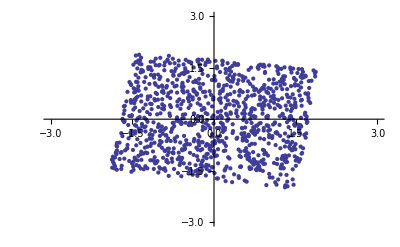

```mathematica
za=Transpose[zmat];
ListPlot[{za[[All]]},PlotRange->{{-3,3},{-3,3}}]
```

```mathematica
w={1,0};
(*w={2,20};//N*)
(*w=w/Norm[w]//N*)
epsilon=0.00001;
n=Length[x];
cnt=1;
wbefore=w;
While[cnt<n,
wbefore=w;
w=(1/n)*Sum[((w.zmat[[All,i]])^3)*zmat[[All,i]],{i,1,n}]-3*w;
w=w/Norm[w];
Print["cnt=",cnt];
Print["w=",w];
If[1-epsilon<=Abs[w.wbefore]&& Abs[w.wbefore]<=1+epsilon,
Print["収束した:"];
Print["w=",w];
Print["cnt=",cnt];
Print["Abs[w.wbefore]=",Abs[w.wbefore]];
cnt=n;
];
++cnt;
]
Kurtosis[w.zmat]-3
```

cnt=1

w={-0.988186,0.153262}

cnt=2

w={0.988056,-0.154096}

収束した:

w={0.988056,-0.154096}

cnt=2

Abs[w.wbefore]=1.

-1.1962

```mathematica
(* True Value*)
tmat=vmat.A;
truemat={};
i=1;
While[i≤2,
truemat=Append[truemat,tmat[[All,i]]/Norm[tmat[[All,i]]]];
i++;
];
truemat=Transpose[truemat];
MatrixForm[truemat]
```

(0.136797 | 0.987876
0.990599 | -0.155248)

2.初期値を変更

```mathematica
w=RandomReal[{-Sqrt[3],Sqrt[3]},2];
(*w={1,0};*)

(*w={2,20};//N*)

(*w=w/Norm[w]//N*)
epsilon=0.00001;
n=Length[x];
cnt=1;
wbefore=w;
While[cnt<n,
wbefore=w;
w=(1/n)*Sum[((w.zmat[[All,i]])^3)*zmat[[All,i]],{i,1,n}]-3*w;
w=w/Norm[w];
Print["cnt=",cnt];
Print["w=",w];
If[1-epsilon<=Abs[w.wbefore]&& Abs[w.wbefore]<=1+epsilon,
Print["収束した:"];
Print["w=",w];
Print["cnt=",cnt];
Print["Abs[w.wbefore]=",Abs[w.wbefore]];
cnt=n
];
++cnt;
];
Kurtosis[w.zmat]-3
```

cnt=1

w={-0.735389,0.677645}

cnt=2

w={0.863219,-0.50483}

cnt=3

w={-0.968373,0.249509}

cnt=4

w={0.987393,-0.158286}

cnt=5

w={-0.988045,0.154167}

収束した:

w={-0.988045,0.154167}

cnt=5

Abs[w.wbefore]=0.999991

-1.19619

```mathematica
MatrixForm[truemat]
```

(0.136797 | 0.987876
0.990599 | -0.155248)

```mathematica
cnt=1;
SignalReshapemat={};
```

```mathematica
While[cnt<=n,
SignalReshapemat=Append[SignalReshapemat,w.zmat[[All,cnt]]];
cnt++;
]
```

```mathematica
x;
y-SignalReshapemat;
```

```mathematica
w.zmat[[All,4]]
```

1.00663

```mathematica
w.vmat.A
```

{0.0176649,-0.994981}